```mathematica
f[x_] := a*(1/(1+x))+b*(1/(2+x))+c*(1/(3+x))+d*(1/(4+x))+e*(1/(5+x))
```

```mathematica
sol = Solve[{f[0]==0.1,f[2]==0.009,f[4]==0.0011,f[6]==0.00003,f[8]==0.0000012},{a,b,c,d,e}]
```

{{a→0.0808615,b→1.43511,c→-4.1306,d→2.95836,e→-0.305696}}

```mathematica
f[x_] = f[x]/.sol[[1]]
```

0.0808615/(1+x)+1.43511/(2+x)-4.1306/(3+x)+2.95836/(4+x)-0.305696/(5+x)

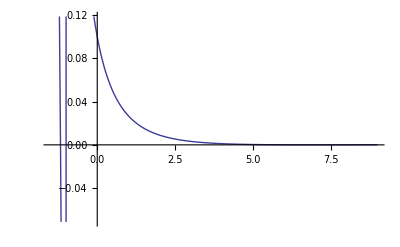

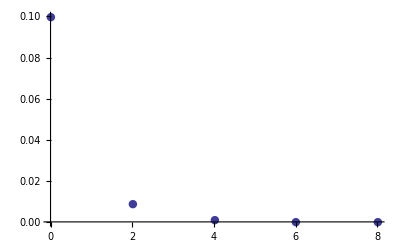

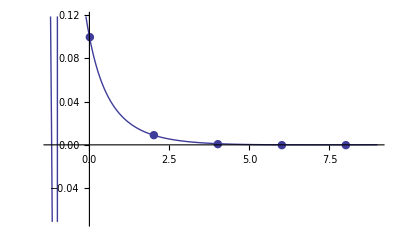

```mathematica
plot1 = Plot[f[x],{x,-1.5,9}]
plot2 = ListPlot[{{0,0.1},{2,0.009},{4,0.0011},{6,0.00003},{8,0.0000012}},PlotMarkers->●]
Show[plot1,plot2,PlotRange->All]
```